# Figure 4

```mathematica
SetDirectory[NotebookDirectory[]];
```

All data were generated with julia code https://github.com/djuliannader/RabiModel.git

#### (a)

```mathematica
Datratio={{0.4,1.4010043181185432/(3*0.6842257819833207^2)},{0.7,1.4461317842084291/(3*0.6952353189666581^2)},{0.71,1.5419684529815025/(3*0.7182764338653959^2)},{0.715,2.0647788577794306/(3*0.8386441314345895^2)},{0.7155,2.3828113293962296/(3*0.9088591107475178^2)},{0.716,3.1910527741596697/(3*1.0807581600041647^2)},{0.7165,7.068549248089215/(3*1.8381566740804358^2)},{0.7167,12.540447165722908/(3*2.8040991976189904^2)},{0.7168,4.281019927997758/(3*0.8331672780526546^2)},{0.717,1.1560381510015576/(3*0.4126601010748559^2)},{0.7175,0.5702496680115973/(3*0.442597016092312^2)},{0.718,0.7596456513036592/(3*0.5130825613153219^2)},{0.72,1.0910956685142317/(3*0.6071421657007087^2)},{0.725,1.265498232158122/(3*0.649448644406925^2)},{0.73,1.306499812187182/(3*0.6605747402037189^2)},{0.75,1.3492500474141749/(3*0.6714095041954184^2)},{0.8,1.3626708346721494/(3*0.6747541511553297^2)},{0.85,1.3615819751736336/(3*0.6744819090091697^2)},{0.9,1.356876757449545/(3*0.6733080037279427^2)},{0.95,1.3498927142878474/(3*0.6715449742973326^2)},{1,1.340308751699645/(3*0.6691860193491785^2)},{1.05,1.3280017701194085/(3*0.6660914741329409^2)},{1.1,1.3117326149310296/(3*0.6619873258758402^2)},{1.15,1.2896672431432579/(3*0.656385942090696^2)},{1.2,1.258419295724224/(3*0.6483805888350059^2)},{1.25,1.2111689697368238/(3*0.6361069192474051^2)},{1.28,1.1692858363608936/(3*0.6250508856572903^2)},{1.3,1.1319757914233515/(3*0.615056513422879^2)},{1.32,1.0831293080462245/(3*0.6017554866146458^2)},{1.34,1.016513906929292/(3*0.5831981734373697^2)},{1.36,0.9205470440964587/(3*0.5555418265449246^2)},{1.38,0.7715882560971632/(3*0.5101049787384198^2)},{1.4,0.5203437591630683/(3*0.42355621883218825^2)},{1.42,0.33996343882151553/(3*0.2707937926473275^2)},{1.44,2.9255481197342186/(3*1.1624342844485611^2)},{1.46,9.386477831912876/(3*1.7939806141073507^2)},{1.48,3.202853387494719/(3*1.0216612478118434^2)},{1.5,2.421434277964104/(3*0.898492341570884^2)},{1.55,1.928557166108979/(3*0.8032728100504959^2)},{1.7,1.6434097025471595/(3*0.7413138777878724^2)},{2,1.5413902630712417/(3*0.7177503556307167^2)},{2.2,1.519415228279878/(3*0.7125268828099697^2)},{2.4,1.507261124273756/(3*0.709545789446798^2)},{2.6,1.5003111398441953/(3*0.7076390327080909^2)},{2.8,1.500812097052059/(3*0.7063503135732676^2)},{2.85,1.510665718701256/(3*0.7061719159221853^2)},{2.88,1.5684850795271097/(3*0.7070940232200617^2)},{2.89,2.4530029032379472/(3*0.7554803733168849^2)},{2.8915,17.438537320501588/(3*2.041158181497078^2)},{2.895,1.388592649536664/(3*0.7182977929746198^2)},{2.9,1.4168283860417321/(3*0.707661709084062^2)},{2.95,1.475831272542683/(3*0.7055831140143968^2)},{3,1.480878063439686/(3*0.7053537529131758^2)},{3.1,1.4826627959191148/(3*0.7049681268967712^2)},{3.2,1.4824563807095834/(3*0.7046323759013358^2)}};
```

```mathematica
Dataratio=Table[{(2π/(2*4.393835879146564))/Datratio[[i,1]],Datratio[[i,2]]},{i,1,Length[Datratio]}];
```

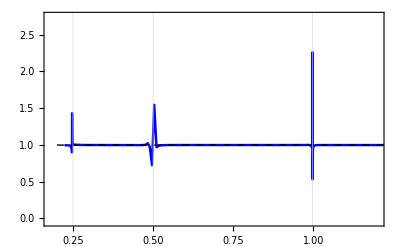

```mathematica
fig4a=Show[ListPlot[Dataratio,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.18,1.2},{-0.05,2.75}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[1.466448498970723/(3*0.7002235674837912^2),{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (b)

```mathematica
Datimp={{0.4,0.9941545393058486},{0.7,0.9940487627989606},{0.71,0.9938517097930761},{0.715,0.9928259803016749},{0.7155,0.9922295277106232},{0.716,0.9907739324098565},{0.7165,0.9844189838590961},{0.7167,0.976428512810312},{0.7168,0.9931069568140486},{0.717,0.9965594057066974},{0.7175,0.9962283682363969},{0.718,0.9956139313816466},{0.72,0.9934136182043649},{0.725,0.9944408247072495},{0.73,0.9943450729406526},{0.75,0.9942519428502714},{0.8,0.994222733074517},{0.85,0.9942246007176634},{0.9,0.9942342717634147},{0.95,0.9942490629681953},{1,0.9942689896520094},{1.05,0.9942952865705182},{1.1,0.9943302802337028},{1.15,0.9943781579643413},{1.2,0.9944467152581313},{1.25,0.9945520035175307},{1.28,0.994646974529722},{1.3,0.9947329114514543},{1.32,0.9948473944341686},{1.34,0.9950073221646286},{1.36,0.9952460878500486},{1.38,0.9956394401383177},{1.4,0.9963926573380568},{1.42,0.9977517493636212},{1.44,0.9899983441080579},{1.46,0.989692106847473},{1.48,0.9912977892879522},{1.5,0.992321459236589},{1.55,0.9931245971085881},{1.7,0.9936511272528142},{2,0.9938521031313995},{2.2,0.9938967797835015},{2.4,0.9939223786126603},{2.6,0.9939389049848489},{2.8,0.9939506946093359},{2.85,0.9939533851274481},{2.88,0.993951225481519},{2.89,0.9936081490783573},{2.8915,0.9836380655279577},{2.895,0.9938308317049003},{2.9,0.993929961881876},{2.95,0.993955064139094},{3,0.993957710097746},{3.1,0.9939614636030565},{3.2,0.9939645620618208}};
```

```mathematica
Dataimp=Table[{(2π/(2*4.393835879146564))/Datimp[[i,1]],1-Datimp[[i,2]]},{i,1,Length[Datimp]}];
```

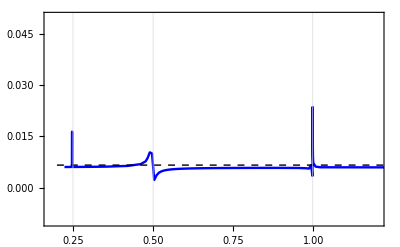

```mathematica
fig4b=Show[ListPlot[Dataimp,Joined->True,PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.18,1.2},{-0.01,0.05}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[1-0.9934136182043661,{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (c)

```mathematica
Datnn={{0.4,1*10^(-10)},{0.7,0},{0.71,0},{0.715,1.6*10^(-6)},{0.7155,0.00029076592523602507},{0.716,0.005590196863773933},{0.7165,0.12408411806264019},{0.7167,0.361350129435033},{0.7168,0.3505284194979199},{0.717,0.12199277461195868},{0.7175,0.007254653582490889},{0.718,0.0006198638561221159},{0.72,1*10^(-12)},{0.725,0},{0.73,0},{0.75,0},{0.8,0},{0.85,0},{0.9,0},{0.95,0},{1.0,5*10^(-9)},{1.05,0},{1.1,0},{1.15,2*10^(-9)},{1.2,1.7*10^(-9)},{1.25,2.7*10^(-9)},{1.28,1.7*10^(-9)},{1.3,1.45*10^(-9)},{1.32,9*10^(-10)},{1.34,2.3*10^(-10)},{1.36,1.1*10^(-11)},{1.38,1.8*10^(-7)},{1.40,0.0002148151597571868},{1.42,0.0616507676777347},{1.44,0.33789819637431735},{1.46,0.21485947757188084},{1.48,0.006226983441246503},{1.5,0.0000016444769232514},{1.55,2*10^(-11)},{1.7,4*10^(-11)},{2,1.5*10^(-11)},{2.2,1.2*10^(-10)},{2.4,1.2*10^(-6)},{2.6,1.2*10^(-10)},{2.8,1.7*10^(-10)},{2.85,2*10^(-9)},{2.88,4.93*10^(-5)},{2.89,0.03471265636315546},{2.8915,0.5481166294059063},{2.895,0.007874676985019091},{2.9,0.0004810471281810891},{2.95,5*10^(-8)},{3,1.7*10^(-8)},{3.1,4*10^(-11)},{3.2,2*10^(-10)}};
```

```mathematica
Dataneg=Table[{(2π/(2*4.393835879146564))/Datnn[[i,1]],Datnn[[i,2]]},{i,1,Length[Datnn]}];
```

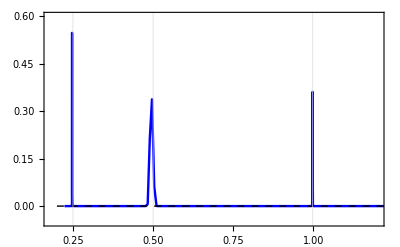

```mathematica
fig4c=Show[ListPlot[Dataneg,Joined->True,PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.18,1.2},{-0.05,0.6}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[00,{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (d)

```mathematica
Datfis={{0.4,1.8188541861330119},{0.7,1.8388028322816627},{0.71,1.874127143527024},{0.715,1.964603626943625},{0.7155,1.9804073771782498},{0.716,1.9723442303712588},{0.7165,1.6912235590856355},{0.7167,1.1296157254529111},{0.7168,1.6922560139343268},{0.717,2.1956940019294273},{0.7175,2.4555613493867083},{0.718,1.3270452941658328},{0.72,1.5501509199699097},{0.725,1.7407462741455948},{0.73,1.766165130060758},{0.75,1.791533329557357},{0.8,1.798893350090337},{0.85,1.7982959049747447},{0.9,1.7957331350439623},{0.95,1.7919587361168188},{1,1.7862909410235246},{1.05,1.7790476173058452},{1.1,1.7689731046925083},{1.15,1.7543659541691137},{1.2,1.7315651395102485},{1.25,1.691319570040237},{1.28,1.6481618171081696},{1.3,1.6018938544201682},{1.32,1.5262648148342361},{1.34,1.3826899818995384},{1.36,1.0338825965291356},{1.38,0.1459688570586324},{1.4,1.6701910152864137},{1.42,1.7890158168263173},{1.44,2.83178092329614},{1.46,3.3271493779904766},{1.48,2.279060956596594},{1.5,2.0845623441769057},{1.55,1.9783566816018272},{1.7,1.908080803068404},{2,1.8761201442897903},{2.2,1.868687381585609},{2.4,1.8648706771509123},{2.6,1.8638288701223988},{2.8,1.8729629122043518},{2.85,1.428141538712384},{2.88,2.0336990375701696},{2.89,3.5792515220462886},{2.8915,3.432645776579064},{2.895,2.141347016678956},{2.9,1.8184114092972472},{2.95,1.8345642774190547},{3,1.8433194470750665},{3.1,1.848268432659257},{3.2,1.8497583055711244}};
```

```mathematica
Datafisher=Table[{(2π/(2*4.393835879146564))/Datfis[[i,1]],Datfis[[i,2]]},{i,1,Length[Datfis]}];
```

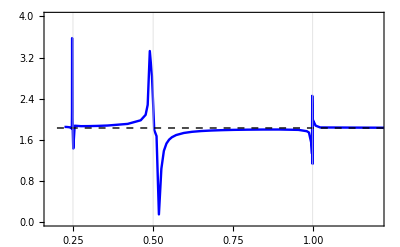

```mathematica
fig4d=Show[ListPlot[Datafisher,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.18,1.2},{0,4}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[1.8283437968627987,{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

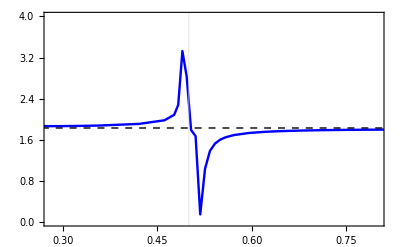

```mathematica
fig4dzoomin=Show[ListPlot[Datafisher,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.28,0.8},{0,4}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[1.8283437968627987,{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

```mathematica
wigner1=Import["wigner_zoomin1.png"];
wigner2=Import["wigner_zoomin2.png"];
wigner3=Import["wigner_zoomin3.png"];
wigner4=Import["wigner_zoomin4.png"];
```

```mathematica
Reswig=Show[fig4dzoomin,Graphics@Inset[wigner1,{0.3,2.2},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner2,{0.57,2.3},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner3,{0.32,0.3},{Left,Bottom},Scaled[0.3]],Graphics@Inset[wigner4,{0.6,0.3},{Left,Bottom},Scaled[0.3]],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.5,2.5},{0.6,2.8}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.51,0.8},{0.42,0.7}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.485,2.5},{0.4,2.6}}]}],Graphics[{Thickness[0.002],Arrowheads[0.035],Arrow[{{0.525,0.8},{0.62,0.85}}]}]]
```

-Graphics-

```mathematica
Export["StructureResonance.png",Reswig]
```

StructureResonance.png

#### (e)

```mathematica
DatexpH0={{0.4,-25.141783302042157},{0.7,-25.14187959260125},{0.71,-25.14176044100161},{0.715,-25.135858983595167},{0.7155,-25.129155045699658},{0.716,-25.10524395557744},{0.7165,-24.919655492938094},{0.7167,-24.5494225580958},{0.7168,-24.566209304699377},{0.717,-24.916742120658352},{0.7175,-25.097286539660953},{0.718,-25.123537605508755},{0.72,-25.13822260636248},{0.725,-25.14089029284121},{0.73,-25.14129514123928},{0.75,-25.141583874091832},{0.8,-25.141653639208336},{0.85,-25.14164895119731},{0.9,-25.14162598914618},{0.95,-25.141589025659254},{1,-25.141535360681715},{1.05,-25.141457662166868},{1.1,-25.141341866993887},{1.15,-25.141160046473477},{1.2,-25.140851388432615},{1.25,-25.14026229362225},{1.28,-25.139605647244114},{1.3,-25.138903751436743},{1.32,-25.137801010695235},{1.34,-25.135917498151233},{1.36,-25.132283300285756},{1.38,-25.12376070866378},{1.4,-25.09500286593096},{1.42,-24.86505946921965},{1.44,-24.623331184264973},{1.46,-24.90060912510621},{1.48,-25.115280750395698},{1.5,-25.13047959935979},{1.55,-25.138434781241838},{1.7,-25.141284800346256},{2,-25.14177271554673},{2.2,-25.14183068472889},{2.4,-25.141855070888763},{2.6,-25.141866818095664},{2.8,-25.141865486249316},{2.85,},{2.88,-25.14132010914874},{2.89,-25.116080531048603},{2.8915,-24.43593684720496},{2.895,-25.134983064972815},{2.9,-25.140778981025072},{2.95,-25.14185578028261},{3,-25.14187248620021},{3.1,-25.141878608928707},{3.2,-25.14188070393656}};
```

```mathematica
DataexpH0=Table[{(2π/(2*4.393835879146564))/DatexpH0[[i,1]],DatexpH0[[i,2]]/50},{i,1,Length[DatexpH0]}];
```

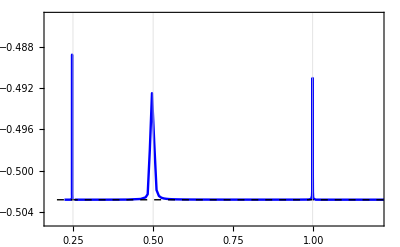

```mathematica
fig4e=Show[ListPlot[DataexpH0,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.18,1.2},{-0.505,-0.485}},GridLines->{{0.25,0.5,0.998},{}},GridLinesStyle->{{Red},{}},Frame->True,LabelStyle->{14,Black}],Plot[-25.142253953183587/50,{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```